### Basic Ideas (03-06)

#### Topology

Starting from a square [0,1]^(×2).

Sphere

```mathematica
Graphics[{Arrowheads[{{0.01,0.5,Arrowhead[]}}],{Arrow[{{0,0},{1,0}}],Text["a",{0.5,0},{0,1}]},
{Arrow[{{0,0},{0,1}}],Text["b",{0,0.5},{2,0}]},
{Arrow[{{1,1},{1,0}}],Text["a",{1,0.5},{-2,0}]},{Arrow[{{1,1},{0,1}}],Text["b",{0.5,1},{0,-1}]}},ImageSize->80]
```

-Graphics-

(x,0)→(1,1-x),
(x,1)→(0,1-x),
(0,y)→(1-y,1),
(1,y)→(1-y,0);
(0,0)=(1,1).

Torus

```mathematica
Graphics[{Arrowheads[{{0.01,0.5,Arrowhead[]}}],{Arrow[{{0,0},{1,0}}],Text["a",{0.5,0},{0,1}]},
{Arrow[{{0,0},{0,1}}],Text["b",{0,0.5},{2,0}]},
{Arrow[{{1,0},{1,1}}],Text["b",{1,0.5},{-2,0}]},{Arrow[{{0,1},{1,1}}],Text["a",{0.5,1},{0,-1}]}},ImageSize->80]
```

-Graphics-

(x,0)→(x,1),
(x,1)→(x,0),
(0,y)→(1,y),
(1,y)→(0,y);
(0,0)=(1,0)=(0,1)=(1,1).

2-Torus

```mathematica
Graphics[{Arrowheads[{{0.01,0.25,Arrowhead[]},{0.01,0.75,Arrowhead[]}}],{Arrow[{{0,0},{1,0}}],Text["a",{0.25,0},{0,1}],
Text["b",{0.75,0},{0,1}]},
{Arrow[{{0,0},{0,1}}],Text["d",{0,0.25},{2,0}],
Text["c",{0,0.75},{2,0}]},
{Arrow[{{1,1},{1,0}}],Text["a",{1,0.25},{-2,0}],
Text["b",{1,0.75},{-2,0}]},{Arrow[{{1,1},{0,1}}],Text["d",{0.25,1},{0,-1}],
Text["c",{0.75,1},{0,-1}]}},ImageSize->80]
```

-Graphics-

(x,0)→Piecewise[{{(1,1/2-x), x≤1/2,}, {(1,3/2-x), x>1/2,}}]
(x,1)→Piecewise[{{(0,1/2-x), x≤1/2,}, {(0,3/2-x), x>1/2,}}]
(0,y)→Piecewise[{{(1/2-y,1), y≤1/2,}, {(3/2-y,1), y>1/2,}}]
(1,y)→Piecewise[{{(1/2-y,0), y≤1/2,}, {(3/2-y,0), y>1/2,}}]
(0,0)=(0,1/2)=(0,1)=(1/2,1)
=(1,1)=(1,1/2)=(1,0)=(1/2,0).

#### Laplacian Modes

Sphere

```mathematica
Block[{L=20,rul,pts,npt,id,Adj,Lap,eigs},
rul={{x_,1}:>{0,1-x},{1,y_}:>{1-y,0}};
pts=Tuples[Range[0,L-1]/L,2];npt=Length@pts;
id=AssociationThread[pts->Range@npt];
Adj=(#+Transpose[#])&@SparseArray[Join@@Table[#->1&/@DeleteCases[id/@{#,#+d//.rul}&/@pts,{_,_Missing}],{d,{{1/L,0},{0,1/L}}}],{npt,npt}];
Lap=SparseArray[Band[{1,1}]->Total/@Adj,{npt,npt}]-Adj;
eigs=SortBy[First]@Thread@Eigensystem[Normal@N@Lap];
Function[{e,v},ListContourPlot[Block[{i=id[#//.rul]},If[MatchQ[i,_Missing],Nothing,Append[#,v⟦i⟧]]]&/@Tuples[Range[0,L]/L,2],Contours->(Range[-1,1,0.2]Max@Abs@v),PlotRangePadding->None,PlotLabel->Chop[e],FrameTicks->None,ImageSize->60]]@@@eigs⟦2;;9⟧
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Torus

```mathematica
Block[{L=20,rul,pts,npt,id,Adj,Lap,eigs},
rul={{x_,1}:>{x,0},{1,y_}:>{0,y}};
pts=Tuples[Range[0,L-1]/L,2];npt=Length@pts;
id=AssociationThread[pts->Range@npt];
Adj=(#+Transpose[#])&@SparseArray[Join@@Table[#->1&/@DeleteCases[id/@{#,#+d//.rul}&/@pts,{_,_Missing}],{d,{{1/L,0},{0,1/L}}}],{npt,npt}];
Lap=SparseArray[Band[{1,1}]->Total/@Adj,{npt,npt}]-Adj;
eigs=SortBy[First]@Thread@Eigensystem[Normal@N@Lap];
Function[{e,v},ListContourPlot[Append[#,v⟦id[#//.rul]⟧]&/@Tuples[Range[0,L]/L,2],Contours->(Range[-1,1,0.2]Max@Abs@v),PlotRangePadding->None,PlotLabel->Chop[e],FrameTicks->None,ImageSize->60]]@@@eigs⟦2;;9⟧
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

2-Torus

```mathematica
Block[{L=36,rul,pts,npt,id,Adj,Lap,eigs},
rul={{x_,1}:>Piecewise[{{{0,1/2-x},x≤1/2},{{0,3/2-x},x>1/2}}],
{1,y_}:>Piecewise[{{{1/2-y,0},y≤1/2},{{3/2-y,0},y>1/2}}]};pts=Tuples[Range[0,L-1]/L,2];npt=Length@pts;
id=AssociationThread[pts->Range@npt];
Adj=(#+Transpose[#])&@SparseArray[Join@@Table[#->1&/@DeleteCases[id/@{#,#+d//.rul}&/@pts,{_,_Missing}],{d,{{1/L,0},{0,1/L}}}],{npt,npt}];
Lap=SparseArray[Band[{1,1}]->Total/@Adj,{npt,npt}]-Adj;
eigs=SortBy[First]@Thread@Eigensystem[Normal@N@Lap];
Function[{e,v},ListContourPlot[Append[#,v⟦id[#//.rul]⟧]&/@Tuples[Range[0,L]/L,2],PlotRange->All,(*Contours->(Range[-1.2,1.2,0.2]Max@Abs@v),*)PlotRangePadding->None,PlotLabel->Chop[e],FrameTicks->None,ImageSize->60]]@@@eigs⟦2;;9⟧
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Game Interface

#### Board

Discretize the unit square into n×n square cells. Each cell is

centered at (x,y)=(i+1/2,j+1/2)/n (i=0:n-1, j=0:n-1)

region relative to center [-1/2,1/2]/n×[-1/2,1/2]/n.

```mathematica
Block[{n=6,cells},
cells=(Tuples[Range[0,n-1],2]+1/2)/n;
Graphics[{{LightGray,Line[{{0,#},{1,#}}&/@(Range[0,n]/n)],
Line[{{#,0},{#,1}}&/@(Range[0,n]/n)]},
Point@cells},ImageSize->120]]
```

-Graphics-

```mathematica
Board[n_]:=<|"n"->n,
"cell"->(AssociationThread[#->Range@Length@#]&[
(Tuples[Range[0,n-1],2]+1/2)/n])|>;
```

```mathematica
board=Board[6]
```

<|n→6,cell→<|{1/12,1/12}→1,{1/12,1/4}→2,{1/12,5/12}→3,{1/12,7/12}→4,{1/12,3/4}→5,{1/12,11/12}→6,{1/4,1/12}→7,{1/4,1/4}→8,{1/4,5/12}→9,{1/4,7/12}→10,{1/4,3/4}→11,{1/4,11/12}→12,{5/12,1/12}→13,{5/12,1/4}→14,{5/12,5/12}→15,{5/12,7/12}→16,{5/12,3/4}→17,{5/12,11/12}→18,{7/12,1/12}→19,{7/12,1/4}→20,{7/12,5/12}→21,{7/12,7/12}→22,{7/12,3/4}→23,{7/12,11/12}→24,{3/4,1/12}→25,{3/4,1/4}→26,{3/4,5/12}→27,{3/4,7/12}→28,{3/4,3/4}→29,{3/4,11/12}→30,{11/12,1/12}→31,{11/12,1/4}→32,{11/12,5/12}→33,{11/12,7/12}→34,{11/12,3/4}→35,{11/12,11/12}→36|>|>

#### Topology

Starting from a square [0,1]^(×2). The topology is defined by the boundary condition.

Sphere

```mathematica
Graphics[{Arrowheads[{{0.01,0.5,Arrowhead[]}}],{Arrow[{{0,0},{1,0}}],Text["a",{0.5,0},{0,1}]},
{Arrow[{{0,0},{0,1}}],Text["b",{0,0.5},{2,0}]},
{Arrow[{{1,1},{1,0}}],Text["a",{1,0.5},{-2,0}]},{Arrow[{{1,1},{0,1}}],Text["b",{0.5,1},{0,-1}]}},ImageSize->80]
```

-Graphics-

(x,0)→(1,1-x),
(x,1)→(0,1-x),
(0,y)→(1-y,1),
(1,y)→(1-y,0);
(0,0)=(1,1).

```mathematica
Board[n_,"sphere"]:=Append[Board[n],
"bc"->{
{x_,0}:>{1,1-x},
{x_,1}:>{0,1-x},
{0,y_}:>{1-y,1},
{1,y_}:>{1-y,0}}];
```

Torus

```mathematica
Graphics[{Arrowheads[{{0.01,0.5,Arrowhead[]}}],{Arrow[{{0,0},{1,0}}],Text["a",{0.5,0},{0,1}]},
{Arrow[{{0,0},{0,1}}],Text["b",{0,0.5},{2,0}]},
{Arrow[{{1,0},{1,1}}],Text["b",{1,0.5},{-2,0}]},{Arrow[{{0,1},{1,1}}],Text["a",{0.5,1},{0,-1}]}},ImageSize->80]
```

-Graphics-

(x,0)→(x,1),
(x,1)→(x,0),
(0,y)→(1,y),
(1,y)→(0,y);
(0,0)=(1,0)=(0,1)=(1,1).

```mathematica
Board[n_,"torus"]:=Append[Board[n],
"bc"->{
{x_,0}:>{x,1},
{x_,1}:>{x,0},
{0,y_}:>{1,y},
{1,y_}:>{0,y}}];
```

2-Torus

```mathematica
Graphics[{Arrowheads[{{0.01,0.25,Arrowhead[]},{0.01,0.75,Arrowhead[]}}],{Arrow[{{0,0},{1,0}}],Text["a",{0.25,0},{0,1}],
Text["b",{0.75,0},{0,1}]},
{Arrow[{{0,0},{0,1}}],Text["d",{0,0.25},{2,0}],
Text["c",{0,0.75},{2,0}]},
{Arrow[{{1,1},{1,0}}],Text["a",{1,0.25},{-2,0}],
Text["b",{1,0.75},{-2,0}]},{Arrow[{{1,1},{0,1}}],Text["d",{0.25,1},{0,-1}],
Text["c",{0.75,1},{0,-1}]}},ImageSize->80]
```

-Graphics-

(x,0)→Piecewise[{{(1,1/2-x), x≤1/2,}, {(1,3/2-x), x>1/2,}}]
(x,1)→Piecewise[{{(0,1/2-x), x≤1/2,}, {(0,3/2-x), x>1/2,}}]
(0,y)→Piecewise[{{(1/2-y,1), y≤1/2,}, {(3/2-y,1), y>1/2,}}]
(1,y)→Piecewise[{{(1/2-y,0), y≤1/2,}, {(3/2-y,0), y>1/2,}}]
(0,0)=(0,1/2)=(0,1)=(1/2,1)
=(1,1)=(1,1/2)=(1,0)=(1/2,0).

```mathematica
Board[n_,"2torus"]:=Append[Board[n],
"bc"->{
{x_,0}:>{1,If[x<1/2,1/2,3/2]-x},
{x_,1}:>{0,If[x<1/2,1/2,3/2]-x},
{0,y_}:>{If[y<1/2,1/2,3/2]-y,1},
{1,y_}:>{If[y<1/2,1/2,3/2]-y,0}}];
```

#### Action Map

Moving towards left, right, down, up by

(x,y)→Piecewise[{{(x-1/n,y), left}, {(x+1/n,y), right}, {(x,y-1/n), down}, {(x,y+1/n), up}}].

Let r_0 and r_1 be the initial an final coordinates. If r_1 falls outside the unit cell, map to the closest cell adjacent to the equivalent point of (r_0+r_1)/2.

```mathematica
ActionMap[board_]:=Block[{n,cell,bc,cmap},
{n,cell,bc}=board/@{"n","cell","bc"};
cmap[d_]:=Table[Block[{r1,x1,y1},
{x1,y1}=r1=r0+d;
cell@r0->cell@If[0<x1<1&&0<y1<1,r1,
Replace[#,{0->1/(2n),1->1-1/(2n)}]&/@
Replace[(r0+r1)/2,bc]]
],{r0,Keys@cell}];
cmap/@<|
"left"->{-1/n,0},
"right"->{1/n,0},
"down"->{0,-1/n},
"up"->{0,1/n}|>]
```

```mathematica
ActionMap@Board[6,"sphere"]
```

<|left→{1→36,2→30,3→24,4→18,5→12,6→6,7→1,8→2,9→3,10→4,11→5,12→6,13→7,14→8,15→9,16→10,17→11,18→12,19→13,20→14,21→15,22→16,23→17,24→18,25→19,26→20,27→21,28→22,29→23,30→24,31→25,32→26,33→27,34→28,35→29,36→30},right→{1→7,2→8,3→9,4→10,5→11,6→12,7→13,8→14,9→15,10→16,11→17,12→18,13→19,14→20,15→21,16→22,17→23,18→24,19→25,20→26,21→27,22→28,23→29,24→30,25→31,26→32,27→33,28→34,29→35,30→36,31→31,32→25,33→19,34→13,35→7,36→1},down→{1→36,2→1,3→2,4→3,5→4,6→5,7→35,8→7,9→8,10→9,11→10,12→11,13→34,14→13,15→14,16→15,17→16,18→17,19→33,20→19,21→20,22→21,23→22,24→23,25→32,26→25,27→26,28→27,29→28,30→29,31→31,32→31,33→32,34→33,35→34,36→35},up→{1→2,2→3,3→4,4→5,5→6,6→6,7→8,8→9,9→10,10→11,11→12,12→5,13→14,14→15,15→16,16→17,17→18,18→4,19→20,20→21,21→22,22→23,23→24,24→3,25→26,26→27,27→28,28→29,29→30,30→2,31→32,32→33,33→34,34→35,35→36,36→1}|>

#### Game Kernel

First create a container to host the game (including the state of the game).

```mathematica
Game[board_]:=Block[{n,cell,amap,agent,food,score},
{n,cell}=board/@{"n","cell"};
amap=ActionMap@board;
{agent,food}=RandomSample[Values@cell,2];
score=n;
<|"board"->board,"amap"->amap,
"state"-><|"agent"->agent,
"food"->food,
"score"->score|>|>];
```

Then specify how the state will be updated based on the action.

```mathematica
Act[game_,action_]:=Block[{agent,food,score},
{agent,food,score}=
game["state"]/@{"agent","food","score"};
agent=Replace[agent,game["amap"][action]];
If[agent==food,
food=RandomChoice[DeleteCases[
Values[game["board"]["cell"]],agent]];
score+=game["board"]["n"],
score-=1];
ReplacePart[game,{"state"}->
<|"agent"->agent,
"food"->food,
"score"->score|>]]
```

Play randomly for 10 steps. Score typically decreases.

```mathematica
#["state"]&/@FoldList[Act,Game@Board[4,"2torus"],RandomChoice[{"left","right","down","up"},10]]
```

{<|agent→1,food→11,score→4|>,<|agent→5,food→11,score→3|>,<|agent→6,food→11,score→2|>,<|agent→10,food→11,score→1|>,<|agent→9,food→11,score→0|>,<|agent→5,food→11,score→-1|>,<|agent→6,food→11,score→-2|>,<|agent→7,food→11,score→-3|>,<|agent→3,food→11,score→-4|>,<|agent→2,food→11,score→-5|>,<|agent→6,food→11,score→-6|>}

#### Game Interface

We can create a game interface for human to play.

```mathematica
Interface[game_]:=Block[{n,cell},
{n,cell}=game["board"]/@{"n","cell"};
Graphics[{
{Green,Translate[Rectangle[{-1,-1}/(2n),{1,1}/(2n)],
Keys[cell]⟦game["state"]["food"]⟧]},
{Red,Translate[Rectangle[{-1,-1}/(2n),{1,1}/(2n)],
Keys[cell]⟦game["state"]["agent"]⟧]},
{Black,AbsoluteThickness[1],
Line[{{0,#},{1,#}}&/@(Range[0,n]/n)],
Line[{{#,0},{#,1}}&/@(Range[0,n]/n)]},
Text[StringTemplate["score: `1`"]
[game["state"]["score"]],
Scaled@{0.5,1},{0,-0.5}]},ImageSize->180]]
```

```mathematica
DynamicModule[{game},
game=Game@Board[10,"torus"];
EventHandler[Dynamic[Interface@game,
TrackedSymbols:>{game}],
{"LeftArrowKeyDown":> {game=Act[game,"left"]},
"RightArrowKeyDown":> {game=Act[game,"right"]},
"DownArrowKeyDown":> {game=Act[game,"down"]},
"UpArrowKeyDown":> {game=Act[game,"up"]}}]]
```

## RL Example

DeviceObject[…]

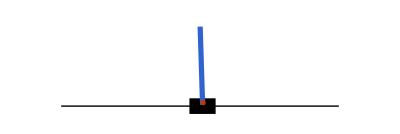

```mathematica
env=DeviceOpen["SimulatedCartPole"]
DeviceExecute[env,"Render"]
```

```mathematica
policyNet=NetInitialize@NetChain[{64,Tanh,2,SoftmaxLayer[]},"Input"->4,"Output"->NetDecoder[{"Class",{Left,Right}}]]
```

NetChain[<>]

```mathematica
reinforceLoss=NetGraph[{CrossEntropyLossLayer["Index"],ThreadingLayer[#1*#2&]},{NetPort["DiscountedReward"]->2,{NetPort["Input"],NetPort["Action"]}->1->2},"Action"->NetEncoder[{"Class",{Left,Right}}]]
```

NetGraph[<>]

```mathematica
discountedSum[rewards_List,gamma_]:=Dot[rewards,gamma^Range[0,Length[rewards]-1]];
applyDiscount[rewards_List,gamma_]:=Table[discountedSum[Drop[rewards,i-1],gamma],{i,Length@rewards}]

CollectEpisodes[env_,policyNet_,totalNumberSteps_Integer,maxStepsPerEp_Integer,discountFactor_]:=Module[{action,actions,epActions,observedState,observedStates,epObservedStates,reward,rewards,discountedRewards,epDiscountedRewards,ended,currentSteps},epActions={};epObservedStates={};epDiscountedRewards={};
currentSteps=0;
(*episode loop*)While[currentSteps<totalNumberSteps,observedStates={};rewards={};actions={};
(*start each new episode with a fresh environment*)observedState=DeviceExecute[env,"Reset"]["ObservedState"];
(*step loop*)Do[AppendTo[observedStates,observedState];
action=policyNet[observedState];
{observedState,reward,ended}=Lookup[DeviceExecute[env,"Step",action],{"ObservedState","Reward","Ended"}];
AppendTo[rewards,reward];
AppendTo[actions,action];
If[ended,Break[]];,Min[maxStepsPerEp,totalNumberSteps-currentSteps]];
discountedRewards=applyDiscount[rewards,discountFactor];
epActions=Join[epActions,actions];
epObservedStates=Join[epObservedStates,observedStates];
epDiscountedRewards=Join[epDiscountedRewards,discountedRewards];
currentSteps+=Length@actions;];
<|"Action"->epActions,"ObservedState"->epObservedStates,"DiscountedReward"->epDiscountedRewards|>];
```

```mathematica
reinforceSampler[env_,net_,batchSize_]:=Block[{data},data=CollectEpisodes[env,net[#,"RandomSample"]&,batchSize,50,0.99];
data["Input"]=data["ObservedState"];
data];
```

```mathematica
reinforceSampler[env,policyNet,2]
```

<|Action→{Right,Left},ObservedState→{{0.0402635,-0.0456719,0.0279923,-0.046689},{0.0393501,0.149038,0.0270586,-0.33041}},DiscountedReward→{1.99,1.},Input→{{0.0402635,-0.0456719,0.0279923,-0.046689},{0.0393501,0.149038,0.0270586,-0.33041}}|>

```mathematica
results=NetTrain[policyNet,reinforceSampler[env,#Net,#BatchSize]&,All,LossFunction->reinforceLoss,Method->"RMSProp",BatchSize->1024,MaxTrainingRounds->50,TrainingProgressMeasurements-><|"Measurement"->NetPort["DiscountedReward"],"Aggregation"->"Mean","Key"->"Reward"|>]
trained=results["TrainedNet"];
```

NetTrain Results
summary | ,,  batches:50  rounds:50  time:24s  examples/s:2220
data | ,,  training examples:1024  processed examples:51200  skipped examples:0
method | ,,  RMSPropoptimizer  batch size1024CPU
round | ,,  loss:1.1×10^1  Reward:2.16×10^1
 | 
 |

```mathematica
DeviceExecute[env,"Reset"];
ListAnimate[Table[(DeviceExecute[env,"Step",DeviceExecute[env,trained[DeviceRead[env]["ObservedState"]]]];
DeviceExecute[env,"Render"]),50]]
```

```mathematica
DeviceExecute[env,"Reset"];
ListAnimate[Table[(DeviceExecute[env,"Step",DeviceExecute[env,"RandomAction"]];
DeviceExecute[env,"Render"]),50]]
```